# SM + sixplet

## Caption

This notebook provides examples illustrating the prediction of unitarity (UNI) and bounded-from-below (BFB) conditions using neural networks for an extension of the Standard Model with an additional 6-dimensional multiplet.
For further details regarding the model, see Refs. https://arxiv.org/abs/2404.07897 and https://arxiv.org/abs/2505.05272

## Initialization Code

Some useful definitions

```mathematica
compTarg="WVM";
compTarg="C";
```

Function for generation of parameters

```mathematica
Clear[genLambdasUNI6plet];
genLambdasUNI6plet=Compile[{},Module[{λ1,λ2,λ3,λ4,λ5,λ6},

λ1=RandomReal[{0,9}];
λ2=RandomReal[{0,10.2}];
λ3=RandomReal[{-7.5,7.5}];
λ4=RandomReal[{-9,9}];
λ5=RandomReal[{-12,8.5}];
λ6=RandomReal[{-15,13}];

{λ1,λ2,λ3,λ4,λ5,λ6}
],CompilationTarget->compTarg];
```

Function that selects data sets according to the UNI conditions

```mathematica
Clear[UniTest6plet];
UniTest6plet=Compile[{{data,_Real,1}},Module[{sqr2=Sqrt[2.],unBound=8.*Pi,unBnd=8.*Pi,
testUn1,testUn2,testUn3,testUn4,testUn5,testUn6,testUn7,testUn8,testUn9,testUn10,test,test0,test1,test2,test3,test4,test5,test6,test7,test8,
λ1,λ2,λ3,λ4,λ5,λ6,λ7,λ8,ξ,λ1a,λ2a,λ3a,λ4a,λ6a,l1,l2,l3,l4,l5,l6,n,p,lmdT1,lmdT2,tabl0=Table[0.,{6}]},

testUn1=testUn2=testUn3=testUn4=testUn5=testUn6=testUn7=testUn8=testUn9=False;
test=test0=test1=test2=test3=test4=test5=test6=test7=test8=False;

{λ1,λ2,λ3,λ4,λ5,λ6}=data;
{λ1a,λ2a,λ3a,λ4a}=Abs/@{λ1,λ2,λ3,λ4};
{l1,l2,l3,l4,l5,l6}=data;

n=6; p=(n-1)/4; 
(*----------------------Uni1-------------------------*)
If[And[Abs[l1]<unBound,Abs[l2]<unBound,Abs[l3]+(n-1)/4*Abs[l4]<unBound,Abs[l3]+(n+1)/4*Abs[l4]<unBound],test1=True,Return[tabl0]];

(*----------------------Uni2-------------------------*)
If[And[Abs[l2+2*l5]<unBound,Abs[l2+2*l6]<unBound,Abs[l2+79/45*l5-22/35*l6]<unBound,Abs[l2+19/9*l5-2/7*l6]<unBound,Abs[l2-29/15*l5+46/35*l6]<unBound,Abs[l2+5/9*l5+10/7*l6]<unBound],test2=True,Return[tabl0]];

(*----------------------Uni3-------------------------*)
lmdT1=-22/15*l5-62/35*l6; lmdT2=14/3*l5+2*l6; 
If[And[Abs[l1+l2+lmdT1]+Sqrt[(l1-(l2+lmdT1))^2+1/6*n*(n^2-1)*l4^2]<2*unBound,
Abs[3*l1+(n+1)*l2+lmdT2]+Sqrt[(3*l1-((n+1)*l2+lmdT2))^2+8*n*l3^2]<2*unBound],test3=True,Return[tabl0]];

test=And[test1,test2,test3];
If[test,data,tabl0]

],CompilationTarget->compTarg];
```

Function that selects data sets according to the BFB conditions

```mathematica
Clear[BFBTest6plet];
BFBTest6plet=Compile[{{data,_Real,1}},Module[{sq2=Sqrt[2],unBnd=8*Pi,λ1,λ2,λ2p,λ3,λ4,λ5,λ6,γ6,γ5,ρ,ζ,λ21,λ22,λ23,λ24,λ1a,λ2a,λ3a,λ4a,Λ,K,S,a,b,c,d,e,α,β,μ,term1,term2,testUn1,testUn2,testUn3,testUn4,testUn5,testUn6,testUn7,testUn8,testUn9,testUn10,test,test0,test1,test2,test3,test4,test5,test6,test7,test8,tabl0=Table[0.,{6}]},
test=test0=test1=test2=test3=test4=False;

testUn1=testUn2=testUn3=testUn4=testUn5=testUn6=testUn7=testUn8=testUn9=False;
test=test0=test1=test2=test3=test4=test5=test6=test7=test8=False;

{λ1,λ2,λ3,λ4,λ5,λ6}=data;
{λ1a,λ2a,λ3a,λ4a}=Abs/@{λ1,λ2,λ3,λ4};

(*----------------------BFB1-------------------------*)
ρ=(5*(1361+288*√5))/(7*109^2); ζ=(20*(1607+471*√5))/(9*109^2);
λ21=λ2+8/9*λ5; λ22=λ2+2*ζ*λ5+2*ρ*λ6; λ23=λ2+89/90*λ5+9/35*λ6; λ24=λ2+5/18*λ5+5/7*λ6;
If[And[λ1>=0,λ2>=0,λ21>=0,λ22>=0,λ23>=0,λ24>=0],test3=True,Return[tabl0]];

(*----------------------BFB2-------------------------*)
If[And[λ3+√(λ1 λ2)-5/4 λ4a>=0,λ3+√(λ1 λ21)-3/4 λ4a>=0,λ3+√(λ1 λ22)-(5 (24 √5-41))/436 λ4a>=0,λ3+√(λ1 λ23)>=0,λ3+√(λ1 λ24)>=0],test4=True,Return[tabl0]];

(*----------------------BFB3-------------------------*)
If[Or[7*λ5+9*λ6>=0,7*(5*√5-8)*λ5-54*λ6>=0,λ21+2/7*λ6+(14*λ5^2)/(9*(14*λ5+9*λ6))>=0],test5=True,Return[tabl0]];

Λ=14*λ5+9*λ6;

(*----------------------BFB4-------------------------*)
a=1./4; b=25.; c=36.; d=2. λ5; e=1. λ2; α=0.; β=4./9;
If[Or[d λ1+a^2 c λ4^2>=0,b d+c e<=0,(a c λ4a)/(√(b-c α))+(d √λ1)/(√(e+d α))>=0,(a c λ4a)/(√(b-c β))+(d √λ1)/(√(e+d β))<=0,λ3+√(((b d+c e) (d λ1+a^2 c λ4^2))/(c d))>=0],test4=True,Return[tabl0]];

a=1/4; b=(225 (2999-912 √5))/39961; c=70/9 b; d=(7 (71677-38000 √5))/119883 λ5+2 λ6; e=λ2+(25 (6485+4104 √5))/359649 λ5; α=ρ; β=9/70;
If[Or[d λ1+a^2 c λ4^2>=0,b d+c e<=0,(a c λ4a)/(√(b-c α))+(d √λ1)/(√(e+d α))>=0,λ3+√(((b d+c e) (d λ1+a^2 c λ4^2))/(c d))>=0],test4=True,Return[tabl0]];

a=1/4; b=25; c=70; d=7/9 λ5+2 λ6; e=λ2; α=0; β=5/14;
If[Or[d λ1+a^2 c λ4^2>=0,b d+c e<=0,(a c λ4a)/(√(b-c α))+(d √λ1)/(√(e+d α))>=0,λ3+√(((b d+c e) (d λ1+a^2 c λ4^2))/(c d))>=0],test4=True,Return[tabl0]];

(*----------------------BFB4-------------------------*)
K=2 (7 λ5+3 λ6)^2+7 λ2 Λ;
S=63 λ4^2+2 λ1 Λ;
μ=(7 λ5)/Λ-(9 λ4a)/Λ √((7 K)/(2 S));
If[Or[Λ>=-2/7 (7 λ5+3 λ6)^2/λ2,Λ>=-63/2 λ4^2/λ1,λ4a<=2/63 √(λ1/λ22) (7 λ5-Λ √(1-7 ρ)),λ4a>=-2/63 √(λ1/λ21) (7 λ5+9 λ6),λ3-(4 μ-1)/4 λ4a>=-√(λ1 (λ2+4/9 λ5+2/63 Λ+4/9 μ λ5-(2 Λ)/63 μ^2))],test6=True,Return[tabl0]];

data
],RuntimeAttributes->{Listable},CompilationOptions->{"InlineExternalDefinitions"->True}, Parallelization->True,CompilationTarget->compTarg];
```

Function that selects data sets according to the UNI + BFB conditions

```mathematica
Clear[UniBFBTest6plet];
UniBFBTest6plet=Compile[{{data,_Real,1}},Module[{sq2=Sqrt[2],unBound=8*Pi,λ1,λ2,λ2p,λ3,λ4,λ5,λ6,γ6,γ5,ρ,ζ,λ21,λ22,λ23,λ24,λ1a,λ2a,λ3a,λ4a,l1,l2,l3,l4,l5,l6,lmdT1,lmdT2,n,p,Λ,K,S,a,b,c,d,e,α,β,μ,term1,term2,testUn1,testUn2,testUn3,testUn4,testUn5,testUn6,testUn7,testUn8,testUn9,testUn10,test,test0,test1,test2,test3,test4,test5,test6,test7,test8,tabl0=Table[0.,{6}]},
test=test0=test1=test2=test3=test4=False;

testUn1=testUn2=testUn3=testUn4=testUn5=testUn6=testUn7=testUn8=testUn9=False;
test=test0=test1=test2=test3=test4=test5=test6=test7=test8=False;

{λ1,λ2,λ3,λ4,λ5,λ6}=data;
{λ1a,λ2a,λ3a,λ4a}=Abs/@{λ1,λ2,λ3,λ4};
{l1,l2,l3,l4,l5,l6}=data;

n=6; p=(n-1)/4; 

(*----------------------Uni1-------------------------*)
If[And[Abs[l1]<unBound,Abs[l2]<unBound,Abs[l3]+(n-1)/4*Abs[l4]<unBound,Abs[l3]+(n+1)/4*Abs[l4]<unBound],test1=True,Return[tabl0]];

(*----------------------Uni2-------------------------*)
If[And[Abs[l2+2*l5]<unBound,Abs[l2+2*l6]<unBound,Abs[l2+79/45*l5-22/35*l6]<unBound,Abs[l2+19/9*l5-2/7*l6]<unBound,Abs[l2-29/15*l5+46/35*l6]<unBound,Abs[l2+5/9*l5+10/7*l6]<unBound],test2=True,Return[tabl0]];

(*----------------------Uni3-------------------------*)
lmdT1=-22/15*l5-62/35*l6; lmdT2=14/3*l5+2*l6; 
If[And[Abs[l1+l2+lmdT1]+Sqrt[(l1-(l2+lmdT1))^2+1/6*n*(n^2-1)*l4^2]<2*unBound,
Abs[3*l1+(n+1)*l2+lmdT2]+Sqrt[(3*l1-((n+1)*l2+lmdT2))^2+8*n*l3^2]<2*unBound],test3=True,Return[tabl0]];


(*----------------------BFB1-------------------------*)
ρ=(5*(1361+288*√5))/(7*109^2); ζ=(20*(1607+471*√5))/(9*109^2);
λ21=λ2+8/9*λ5; λ22=λ2+2*ζ*λ5+2*ρ*λ6; λ23=λ2+89/90*λ5+9/35*λ6; λ24=λ2+5/18*λ5+5/7*λ6;
If[And[λ1>=0,λ2>=0,λ21>=0,λ22>=0,λ23>=0,λ24>=0],test3=True,Return[tabl0]];

(*----------------------BFB2-------------------------*)
If[And[λ3+√(λ1 λ2)-5/4 λ4a>=0,λ3+√(λ1 λ21)-3/4 λ4a>=0,λ3+√(λ1 λ22)-(5 (24 √5-41))/436 λ4a>=0,λ3+√(λ1 λ23)>=0,λ3+√(λ1 λ24)>=0],test4=True,Return[tabl0]];

(*----------------------BFB3-------------------------*)
If[Or[7*λ5+9*λ6>=0,7*(5*√5-8)*λ5-54*λ6>=0,λ21+2/7*λ6+(14*λ5^2)/(9*(14*λ5+9*λ6))>=0],test5=True,Return[tabl0]];

Λ=14*λ5+9*λ6;

(*----------------------BFB4-------------------------*)
a=1./4; b=25.; c=36.; d=2. λ5; e=1. λ2; α=0.; β=4./9;
If[Or[d λ1+a^2 c λ4^2>=0,b d+c e<=0,(a c λ4a)/(√(b-c α))+(d √λ1)/(√(e+d α))>=0,(a c λ4a)/(√(b-c β))+(d √λ1)/(√(e+d β))<=0,λ3+√(((b d+c e) (d λ1+a^2 c λ4^2))/(c d))>=0],test4=True,Return[tabl0]];

a=1/4; b=(225 (2999-912 √5))/39961; c=70/9 b; d=(7 (71677-38000 √5))/119883 λ5+2 λ6; e=λ2+(25 (6485+4104 √5))/359649 λ5; α=ρ; β=9/70;
If[Or[d λ1+a^2 c λ4^2>=0,b d+c e<=0,(a c λ4a)/(√(b-c α))+(d √λ1)/(√(e+d α))>=0,λ3+√(((b d+c e) (d λ1+a^2 c λ4^2))/(c d))>=0],test4=True,Return[tabl0]];

a=1/4; b=25; c=70; d=7/9 λ5+2 λ6; e=λ2; α=0; β=5/14;
If[Or[d λ1+a^2 c λ4^2>=0,b d+c e<=0,(a c λ4a)/(√(b-c α))+(d √λ1)/(√(e+d α))>=0,λ3+√(((b d+c e) (d λ1+a^2 c λ4^2))/(c d))>=0],test4=True,Return[tabl0]];

(*----------------------BFB4-------------------------*)
K=2 (7 λ5+3 λ6)^2+7 λ2 Λ;
S=63 λ4^2+2 λ1 Λ;
μ=(7 λ5)/Λ-(9 λ4a)/Λ √((7 K)/(2 S));
If[Or[Λ>=-2/7 (7 λ5+3 λ6)^2/λ2,Λ>=-63/2 λ4^2/λ1,λ4a<=2/63 √(λ1/λ22) (7 λ5-Λ √(1-7 ρ)),λ4a>=-2/63 √(λ1/λ21) (7 λ5+9 λ6),λ3-(4 μ-1)/4 λ4a>=-√(λ1 (λ2+4/9 λ5+2/63 Λ+4/9 μ λ5-(2 Λ)/63 μ^2))],test6=True,Return[tabl0]];

data
],RuntimeAttributes->{Listable},CompilationOptions->{"InlineExternalDefinitions"->True}, Parallelization->True,CompilationTarget->compTarg];
```

Function that minimizes the potential V_4  in all directions of the real fields.

```mathematica
Clear[PotFunc6plet,Minim6pletFunc];
PotFunc6plet=Compile[{{param1,_Real,1},{param2,_Real,1}},Module[{λ1,λ2,λ3,λ4,λ5,λ6,c,d,e,f,g,h},

{λ1,λ2,λ3,λ4,λ5,λ6}=param1;
{c,d,e,f,g,h}=param2;

λ1/2+1/2 (c^2+d^2+e^2+f^2+g^2+h^2)^2 λ2+(c^2+d^2+e^2+f^2+g^2+h^2) λ3+1/4 (-5 c^2-3 d^2-e^2+f^2+3 g^2+5 h^2) λ4+1/45 (20 d^4+12 e^4+12 f^4+6 e^2 g^2+20 g^4-10 √5 f g (3 e+2 √2 g) h+75 e^2 h^2-8 c e (3 √5 e g+5 f h)+5 c^2 (10 e^2+15 f^2+12 g^2+5 h^2)+f^2 (16 e^2-12 √2 e g+15 g^2+50 h^2)+d^2 (5 e (-4 √10 c+3 e)+6 f^2+49 g^2+60 h^2)-2 d (6 √2 e^2 f+28 e f g+12 √5 f^2 h-6 √10 e g h+c (15 √5 e f-6 √10 f g-35 g h))) λ5+1/35 (9 e^4+9 f^4+2 e^2 (-12 √2 d f+f^2+6 √5 c g+16 g^2)-4 d (4 √10 c f g-3 √5 f^2 h+15 c g h)+10 c^2 (2 g^2+5 h^2)+2 d^2 (16 f^2+9 g^2+10 h^2)-4 e (d g (3 f+4 √10 h)+f (6 √2 f g-5 c h))) λ6

],RuntimeAttributes->{Listable},CompilationOptions->{"InlineExternalDefinitions"->True}(*, Parallelization->True*),CompilationTarget->compTarg];

Minim6pletFunc[parameters_]:=Module[{bndT=10^2,λ1,λ2,λ3,λ4,λ5,λ6,minFunc,minPotVal,c,d,e,f,g,h,parBounds,parRegion},

{λ1,λ2,λ3,λ4,λ5,λ6}=parameters;

parRegion={c,d,e,f,g,h};
parBounds=(-bndT≤#≤bndT)&/@parRegion;

minPotVal=NMinimize[{PotFunc6plet[{λ1,λ2,λ3,λ4,λ5,λ6},{c,d,e,f,g,h}],parBounds},parRegion,Method->{"NelderMead","RandomSeed"->RandomInteger[{1,1000}]}];
If[First[minPotVal]>0,
minPotVal=NMinimize[{PotFunc6plet[{λ1,λ2,λ3,λ4,λ5,λ6},{c,d,e,f,g,h}],parBounds},parRegion,Method->{"DifferentialEvolution","PostProcess"->{FindMinimum,Method->"PrincipalAxis"},"RandomSeed"->RandomInteger[{1,1000}],(*"SearchPoints"->100,*)"CrossProbability"->RandomReal[{0.5,0.9}],"ScalingFactor"->RandomReal[{0.5,0.9}]}]];

{First[minPotVal],parameters,parRegion}/.Last[minPotVal]

];
```

## Numerical computations

### Parameters of the potential

The datasets which obey only UNI conditions

```mathematica
zeroTabl=Table[0.,{6}]; 
valUNIlmd=ParallelTable[
valTMP=zeroTabl;
While[valTMP==zeroTabl,
pointRND=genLambdasUNI6plet[];
valTMP=UniTest6plet[pointRND];
];
valTMP
,{10^3}];//AbsoluteTiming
```

{0.038074,Null}

The datasets which obey UNI+BFB conditions

```mathematica
zeroTabl=Table[0.,{6}]; 
valUniBFBlmd=ParallelTable[
valTMP=zeroTabl;
While[valTMP==zeroTabl,
valTMP1=zeroTabl;
While[valTMP1==zeroTabl,
pointRND=genLambdasUNI6plet[];
valTMP1=UniTest6plet[pointRND];
];
valTMP=BFBTest6plet[pointRND];
];
valTMP
,{10^6}];//AbsoluteTiming
```

{31.0873,Null}

Lets  check computed datasets

```mathematica
DeleteCases[Table[UniBFBTest6plet[valUniBFBlmd[[x]]],{x,1,10^6}],zeroTabl]//Length
```

1000000

```mathematica
Export[NotebookDirectory[]<>"data/goodData_6plet.dat",valUniBFBlmd⟦;;⟧,"Data"]
```

The ranges of the parameters

```mathematica
lmdNames={"λ_1","λ_2","λ_3","λ_4","λ_5","λ_6"};
TableForm[(MinMax/@Transpose@#),TableHeadings->{lmdNames,{"Min","Max"}}]&/@{valUniBFBlmd};
Grid[{%},Spacings->{3, 0}]
```

| Min | Max
λ_1 | 7.16671×10^-6 | 8.37684
λ_2 | 0.000029631 | 9.79165
λ_3 | -2.99861 | 6.97221
λ_4 | -6.2168 | 6.21159
λ_5 | -8.95293 | 6.27541
λ_6 | -9.10834 | 11.9642

### Minimization of the potential V_4

Perform global minimization of the potential V_4 under various boundary conditions for the fields to find 1000 points which satisfy UNI and BFB conditions

```mathematica
zeroTabl=Table[0.,{6}];
minTestList=ParallelTable[
minPotVal1=-1;
While[minPotVal1<0,
valTMP=zeroTabl;
While[valTMP==zeroTabl,
lmdT=genLambdasUNI6plet[];
valTMP=UniTest6plet[lmdT];
];
(minPotVal=Minim6pletFunc[valTMP])//Quiet;
minPotVal1=First@minPotVal;
];
minPotVal
,{1000}];//AbsoluteTiming
```

{496.028,Null}

Let’s  check computed datasets

```mathematica
DeleteCases[UniTest6plet/@minTestList⟦;;,2⟧,zeroTabl]//Length
DeleteCases[UniBFBTest6plet[#]&/@minTestList⟦;;,2⟧,zeroTabl]//Length
```

1000

997

## Nets training

### Training data

generation of raw  data

```mathematica
zeroTabl=Table[0.,{6}];
dataT107=ParallelTable[
pointRND=genLambdasUNI6plet[];
valTMP=If[UniBFBTest6plet[pointRND]==zeroTabl,0,1];
pointRND->valTMP
,{10^7}];//AbsoluteTiming
```

{18.5699,Null}

points which obey UNI+BFB conditions in raw data

```mathematica
Count[dataT107⟦;;,2⟧,1]
%/Length[dataT107]*100//N
```

32736

0.32736

loading  dataset with “good” data, which obey UNI+BFB conditions generated previously

```mathematica
valUniBFBlmd=ToExpression@Import[NotebookDirectory[]<>"data/goodData_6plet.dat","Data"];
```

```mathematica
badDataG=Select[dataT107,#⟦2⟧==0&]⟦;;,1⟧;
%//Length
goodDataG=valUniBFBlmd;
```

9967264

trainingData with 10% of good points. Such combination is the most effective to train the first net.

```mathematica
trainingData=RandomSample@Join[Rule[#,0]&/@badDataG⟦;;⟧,Rule[#,1]&/@goodDataG⟦;;⟧];
Count[trainingData⟦;;,2⟧,1]
%/Length[dataT107]*100//N
```

1000000

10.

definition of decoder

```mathematica
dec=NetDecoder[{"Class",{0,1}}];
```

### net-1 (128 neurons)

definition  of net-1

```mathematica
netOne=NetInitialize[NetChain[{128,Ramp,128,Ramp,128,Ramp,2,SoftmaxLayer[]},"Output"->dec,"Input"->5],Method->{"Xavier","FactorType"->"Mean"}];
```

training of net-1 with trainingData dataset

```mathematica
trainPart=IntegerPart[Length[trainingData]*0.9];
timeStart=AbsoluteTime[];
trainedNet1=NetTrain[netOne,trainingData⟦;;trainPart⟧,BatchSize->2^14,ValidationSet->trainingData⟦trainPart;;⟧,TargetDevice->"GPU",Method->"RMSProp",(*WorkingPrecision->"Real32"*)WorkingPrecision->"Mixed",MaxTrainingRounds->500(*,LearningRate->0.00025*)];
AbsoluteTime[]-timeStart
```

600.678185

```mathematica
Export[NotebookDirectory[]<>"data/networks/trainedNet1_6plet.wlnet",trainedNet1]
```

### net-2 (256 neurons)

definition  of net-2

```mathematica
netTwo=NetInitialize[NetChain[{256,Ramp,256,Ramp,256,Ramp,2,SoftmaxLayer[]},"Output"->dec,"Input"->5],Method->{"Xavier","FactorType"->"Mean"}];
```

let’s make trainingDataNet1 using net-1

```mathematica
zeroTabl=Table[0.,{6}];
dataTT=ParallelTable[
dataT=Table[genLambdasUNI6plet[],{10^6}];
results=trainedNet1[dataT];
results2=DeleteCases[Thread[dataT->results],_->0];
If[UniBFBTest6plet[#]==zeroTabl,#->0,#->1]&/@results2⟦;;,1⟧
,{3*290}];//AbsoluteTiming
```

{207.416,Null}

let’s  check the ratio of good points

```mathematica
trainingDataNet1=Flatten[dataTT,1];
%//Length
Count[trainingDataNet1⟦;;,2⟧,1]
Count[trainingDataNet1⟦;;,2⟧,1]/Length[trainingDataNet1]//N
```

3047643

2835215

0.930298

we dilute the trainingDataNet1 dataset  to reduce the percentage of good points, if necessary.

```mathematica
trainingDataNet2=RandomSample@Join[Rule[#,0]&/@badDataG,trainingDataNet1];
%//Length
Count[trainingDataNet2⟦;;,2⟧,1]
%/Length[trainingDataNet2]//N
trainPart=IntegerPart[Length[trainingDataNet2]*0.9]
```

13014907

2835215

0.217844

11713416

training of net-2 with trainingDataNet2 dataset

```mathematica
timeStart=AbsoluteTime[];
trainedNet2=NetTrain[netTwo,trainingDataNet2⟦;;trainPart⟧,BatchSize->2^14,ValidationSet->trainingDataNet2⟦trainPart;;⟧,TargetDevice->"GPU",Method->"RMSProp",WorkingPrecision->"Mixed",MaxTrainingRounds->500];
AbsoluteTime[]-timeStart
```

951.969789

```mathematica
Export[NotebookDirectory[]<>"data/networks/trainedNet2_6plet.wlnet",trainedNet2]
```

### net-3 (512 neurons)

definition  of net-3

```mathematica
netThree=NetInitialize[NetChain[{512,Ramp,512,Ramp,512,Ramp,2,SoftmaxLayer[]},"Output"->dec,"Input"->5],Method->{"Xavier","FactorType"->"Mean"}];
```

training of net-3 with trainingDataNet2 dataset

```mathematica
timeStart=AbsoluteTime[];
trainedNet3=NetTrain[netThree,trainingDataNet2⟦;;trainPart⟧,BatchSize->2^14,ValidationSet->trainingDataNet2⟦trainPart;;⟧,TargetDevice->"GPU",Method->"RMSProp",WorkingPrecision->"Mixed",MaxTrainingRounds->500];
AbsoluteTime[]-timeStart
```

1675.37789

```mathematica
Export[NotebookDirectory[]<>"data/networks/trainedNet3_6plet.wlnet",trainedNet3]
```

prediction of UNI+ BFB conditions with net-3

```mathematica
zeroTabl=Table[0.,{6}]; 
dataTT=ParallelTable[
dataT=Table[genLambdasUNI6plet[],{10^6}];
results=trainedNet3[dataT];
results2=DeleteCases[Thread[dataT->results],_->0];
If[UniBFBTest6plet[#]==zeroTabl,#->0,#->1]&/@results2⟦;;,1⟧
,{45}];//AbsoluteTiming
```

{51.4717,Null}

Let us examine the fraction of valid points in the dataset.

```mathematica
dataT3=Flatten[dataTT,1];
%//Length
Count[dataT3⟦;;,2⟧,1]
%/Length[dataT3]//N
```

146784

145432

0.990789

### net-4 (1024 neurons)

definition  of net-4

```mathematica
netFour=NetInitialize[NetChain[{1024,Ramp,1024,Ramp,1024,Ramp,2,SoftmaxLayer[]},"Output"->dec,"Input"->5],Method->{"Xavier","FactorType"->"Mean"}];
```

training of net-4 with trainingDataNet2 dataset

```mathematica
timeStart=AbsoluteTime[];
trainedNet4=NetTrain[netFour,trainingDataNet2⟦;;trainPart⟧,BatchSize->2^14,ValidationSet->trainingDataNet2⟦trainPart;;⟧,TargetDevice->"GPU",Method->"RMSProp",WorkingPrecision->"Mixed",MaxTrainingRounds->500];
AbsoluteTime[]-timeStart
```

3657.536117

```mathematica
Export[NotebookDirectory[]<>"data/networks/trainedNet4_6plet.wlnet",trainedNet4]
```

prediction of UNI+ BFB conditions with net-4

```mathematica
zeroTabl=Table[0.,{6}]; 
dataTT=ParallelTable[
dataT=Table[genLambdasUNI6plet[],{10^6}];
results=trainedNet4[dataT];
results2=DeleteCases[Thread[dataT->results],_->0];
If[UniBFBTest6plet[#]==zeroTabl,#->0,#->1]&/@results2⟦;;,1⟧
,{45}];//AbsoluteTiming
```

{169.174,Null}

Let us examine the fraction of valid points in the dataset.

```mathematica
dataT3=Flatten[dataTT,1];
%//Length
Count[dataT3⟦;;,2⟧,1]
%/Length[dataT3]//N
```

146861

145522

0.990883

## Nets testing

Predictions of net-1

```mathematica
zeroTabl=Table[0.,{6}]; 
dataTT=ParallelTable[
dataT=Table[genLambdasUNI6plet[],{10^6}];
results=trainedNet1[dataT];
results2=DeleteCases[Thread[dataT->results],_->0];
If[UniBFBTest6plet[#]==zeroTabl,#->0,#->1]&/@results2⟦;;,1⟧
,{10}];//AbsoluteTiming
```

{10.6811,Null}

Let us examine the fraction of valid points in the dataset.

```mathematica
dataT3=Flatten[dataTT,1];
%//Length
Count[dataT3⟦;;,2⟧,1]
%/Length[dataT3]//N
```

35083

32677

0.93142

Predictions of net-2

```mathematica
zeroTabl=Table[0.,{6}]; 
dataTT=ParallelTable[
dataT=Table[genLambdasUNI6plet[],{10^6}];
results=trainedNet2[dataT];
results2=DeleteCases[Thread[dataT->results],_->0];
If[UniBFBTest6plet[#]==zeroTabl,#->0,#->1]&/@results2⟦;;,1⟧
,{20}];//AbsoluteTiming
```

{15.3064,Null}

Let us examine the fraction of valid points in the dataset.

```mathematica
dataT3=Flatten[dataTT,1];
%//Length
Count[dataT3⟦;;,2⟧,1]
%/Length[dataT3]//N
```

65462

64955

0.992255

Predictions from the combination of net-1 and net-2

```mathematica
zeroTabl=Table[0.,{6}]; 
dataTT=ParallelTable[
dataT=Table[genLambdasUNI6plet[],{10^6}];
results=trainedNet1[dataT];
results2=DeleteCases[Thread[dataT->results],_->0];
If[Length[results2]==0,results2={zeroTabl->0}];
results=trainedNet2[results2⟦;;,1⟧];
results2=DeleteCases[Thread[results2⟦;;,1⟧->results],_->0];
If[Length[results2]==0,results2={zeroTabl->0}];
If[UniBFBTest6plet[#]==zeroTabl,#->0,#->1]&/@results2⟦;;,1⟧
,{300}];//AbsoluteTiming
```

{78.8309,Null}

Let us examine the fraction of valid points in the dataset.

```mathematica
dataT3=Flatten[dataTT,1];
%//Length
Count[dataT3⟦;;,2⟧,1]
%/Length[dataT3]//N
```

977933

972304

0.994244

Predictions from the combination of net-2, net-3, and net-4

```mathematica
zeroTabl=Table[0.,{6}]; 
dataTT=ParallelTable[
dataT=Table[genLambdasUNI6plet[],{10^6}];
results=trainedNet2[dataT];
results2=DeleteCases[Thread[dataT->results],_->0];
If[Length[results2]==0,results2={zeroTabl->0}];
results=trainedNet3[results2⟦;;,1⟧];
results2=DeleteCases[Thread[results2⟦;;,1⟧->results],_->0];
If[Length[results2]==0,results2={zeroTabl->0}];
results=trainedNet4[results2⟦;;,1⟧];
results2=DeleteCases[Thread[results2⟦;;,1⟧->results],_->0];
If[Length[results2]==0,results2={zeroTabl->0}];
If[UniBFBTest6plet[#]==zeroTabl,#->0,#->1]&/@results2⟦;;,1⟧
,{300}];//AbsoluteTiming
```

{131.2,Null}

Let us examine the fraction of valid points in the dataset.

```mathematica
dataT3=Flatten[dataTT,1];
%//Length
Count[dataT3⟦;;,2⟧,1]
%/Length[dataT3]//N
```

967163

965067

0.997833

Predictions from the combination of net-2, net-3, and net-4 with validation performed by potential minimization

Here, we compute from the raw data using net-2 through net-4, with validation performed by potential minimization. A total of approximately 1000 good points are evaluated.

```mathematica
timeStart=AbsoluteTime[];
zeroTabl=Table[0.,{6}];
dataTT=ParallelTable[
dataT=Table[genLambdasUNI6plet[],{10^4}];
results=trainedNet2[dataT];
results2=DeleteCases[Thread[dataT->results],_->0];
If[Length[results2]==0,results2={zeroTabl->0}];
results=trainedNet3[results2⟦;;,1⟧];
results2=DeleteCases[Thread[results2⟦;;,1⟧->results],_->0];
If[Length[results2]==0,results2={zeroTabl->0}];
results=trainedNet4[results2⟦;;,1⟧];
results2=DeleteCases[Thread[results2⟦;;,1⟧->results],_->0]
,{35}];//AbsoluteTiming

dataT3=DeleteCases[Flatten[dataTT],zeroTabl->_];
tmp=DeleteCases[UniBFBTest6plet/@dataT3[[;;,1]],zeroTabl]//Length;
{Length[dataT3],tmp,tmp/Length[dataT3]//N}

minTestList=ParallelTable[
(minPotVal=Minim6pletFunc[dataT3[[xx,1]]])//Quiet;
minPotVal
,{xx,1,Length[dataT3]}];//AbsoluteTiming
minTestList=DeleteCases[minTestList,{a_/;a<0,_,_}];
%//Length
AbsoluteTime[]-timeStart
```

{0.763419,Null}

{1094,1090,0.996344}

{44.0881,Null}

1093

44.856458

Let us examine the fraction of valid points in the dataset.

```mathematica
DeleteCases[UniBFBTest6plet/@minTestList[[;;,2]],zeroTabl]//Length
%/Length[minTestList]//N
```

1090

0.997255

Classifier Measurements of nets

```mathematica
zeroTabl=Table[0.,{6}];
dataT=ParallelTable[
pointRND=genLambdasUNI6plet[];
valTMP=If[UniBFBTest6plet[pointRND]==zeroTabl,0,1];
pointRND->valTMP
,{10^7}];//AbsoluteTiming
```

{18.0776,Null}

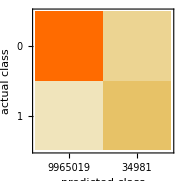
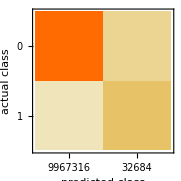
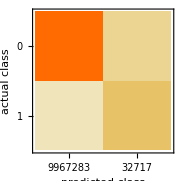
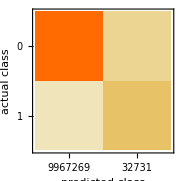
{Classifier Measurements
Classifier method | Net
Number of test examples | 10000000
Accuracy | (99.97550.0005) %
Accuracy baseline | (99.67350.0018) %
Geometric mean of probabilities | 0.999 ± 0.000019
Mean cross entropy | 0.000825 ± 0.000019
Single evaluation time | 3.81 ms/example
Batch evaluation speed | 1.04 examples/μs
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 10000000
Accuracy | (99.995250.00022) %
Accuracy baseline | (99.67350.0018) %
Geometric mean of probabilities | 1. ± 5.4×10^-6
Mean cross entropy | 0.000121 ± 5.4×10^-6
Single evaluation time | 4.2 ms/example
Batch evaluation speed | 847. examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 10000000
Accuracy | (99.994760.00023) %
Accuracy baseline | (99.67350.0018) %
Geometric mean of probabilities | 1. ± 6.6×10^-6
Mean cross entropy | 0.000146 ± 6.6×10^-6
Single evaluation time | 4.26 ms/example
Batch evaluation speed | 401. examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 10000000
Accuracy | (99.994600.00023) %
Accuracy baseline | (99.67350.0018) %
Geometric mean of probabilities | 1. ± 5.6×10^-6
Mean cross entropy | 0.000136 ± 5.6×10^-6
Single evaluation time | 4.08 ms/example
Batch evaluation speed | 159. examples/ms
-Graphics- | }

```mathematica
classfT=ClassifierMeasurements[#,RandomSample[dataT]⟦;;⟧]&/@{trainedNet1,trainedNet2,trainedNet3,trainedNet4}
```